# Tesis de Sara v4.0

## Inicialización

```mathematica
Needs["AdvancedMapping`"];
```

```mathematica
RCM[ca_]:=Block[{n =Length[ca]},N[Abs[1/n Sum[ca[[i]](i-n/2),{i,1,n}]]]];
Returns[x_,Δt_]:= DeleteCases[N[Log[Drop[x,Δt]]-Log[Take[x,{1,-(1+Δt)}]]],Indeterminate];
CATimeSeries[rule_,states_,radius_,size_,iterations_]:=Map[RCM,CellularAutomaton[{rule,states,radius},RandomInteger[states-1,size],iterations]];
```

```mathematica
RCM@RandomInteger[2,10]
```

0.5

```mathematica
Manipulate[ArrayPlot[CellularAutomaton[{r,3,1},RandomInteger[2,100],100]],{r,1,6000,1}]
```

```mathematica
3^2^3
```

6561

```mathematica
RandomInteger[6400,10]
```

{6178,4543,5545,3700,5924,1961,6365,5049,2722,836}

```mathematica
ret = Returns[CATimeSeries[2722,3,1,100,10000],1];
```

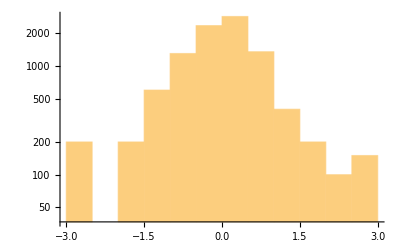

```mathematica
Histogram[ret,ScalingFunctions->"Log"]
```

```mathematica
Clear[HistogramPoints]
```

```mathematica
(* Opciones de estilo *)
smallFontSize = 13;
bigFontSize = 15;
plotSize = 500;
colors = {ColorData["Legacy"]["IndianRed"],Black,Blue,ColorData["Legacy"]["Olive"]};

HistogramPoints[data_,bspec_ : Automatic]:=Transpose[MapAt[Drop[#,1]&,HistogramList[data,bspec,"Count"],1]];
HistogramPointPlot[data_,opts: OptionsPattern[]]:=Block[{pltData = HistogramPoints[data]},
ListPlot[
pltData,
Joined->False,
Frame->True,
PlotTheme->"Monochrome",
BaseStyle->FontSize->14,
PlotStyle->{First[colors],{PointSize[Large],First[colors]}},
ImageSize->500,
PlotMarkers->None,
GridLines->{Automatic,All},
GridLinesStyle->Directive[Gray,Opacity[0.3]],
FilterRules[{opts},Options[ListPlot]]
]
];
```

```mathematica
3^2^3
```

6561

```mathematica
reglasRandom = Sort@RandomInteger[6561-1,100]
```

{64,230,329,407,409,454,466,497,518,525,554,762,815,939,982,1030,1100,1161,1196,1284,1334,1344,1382,1416,1501,1569,1570,1617,1621,1652,1707,1773,1797,1828,1880,1971,2062,2158,2244,2257,2310,2420,2701,2787,2883,2921,3121,3129,3157,3189,3227,3362,3423,3474,3523,3532,3631,3735,3796,3881,3914,4176,4195,4277,4344,4361,4607,4663,4697,4701,4713,4884,5087,5345,5439,5451,5452,5487,5565,5583,5625,5877,5879,5916,5924,5933,5961,6075,6086,6182,6207,6246,6248,6270,6309,6312,6326,6403,6493,6528}

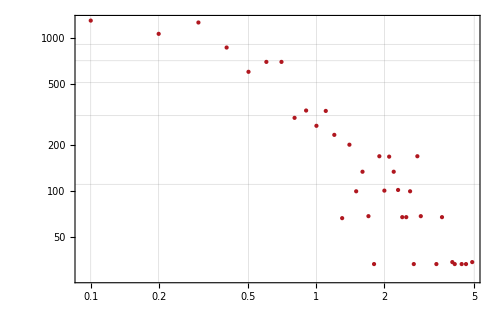

```mathematica
HistogramPointPlot[Abs[Returns[CATimeSeries[5583,3,1,100,10000],1]],ScalingFunctions->{"Log","Log"}]
```

```mathematica
FindDistribution[Abs[Returns[CATimeSeries[5583,3,1,100,10000],1]]]
```

MixtureDistribution[{0.867301,0.132699},{NormalDistribution[0.4625,0.321155],CauchyDistribution[1.58033,0.38778]}]

```mathematica
DistributionFitTest[Abs[Returns[CATimeSeries[5583,3,1,100,10000],1]],ParetoDistribution[a,b]]
```

DistributionFitTest::ntsprt: One or more data points are not in support of the process or distribution ParetoDistribution[a,b].

Indeterminate

```mathematica
ParetoDistribution
```

```mathematica
histogramas = %;
```

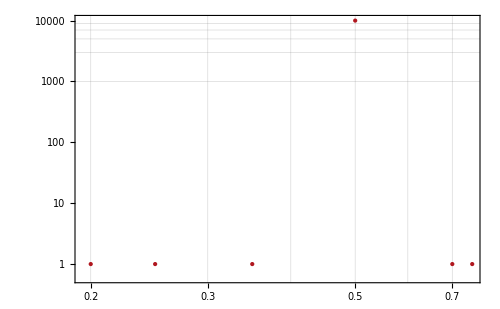
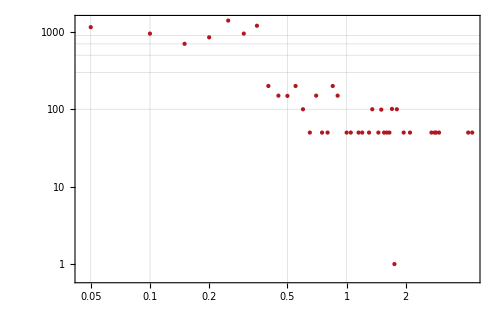
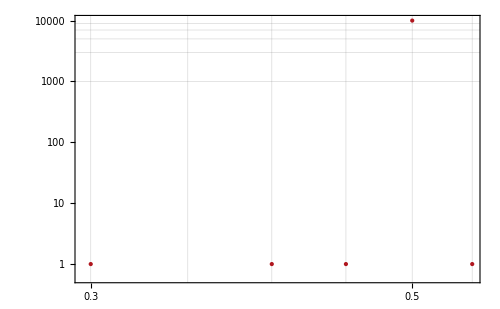
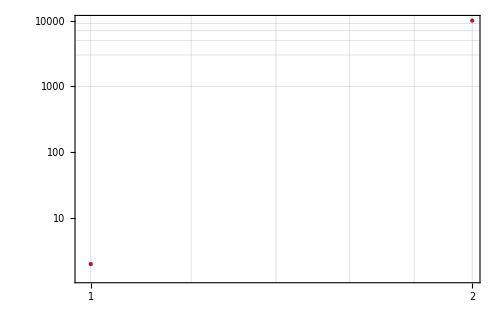
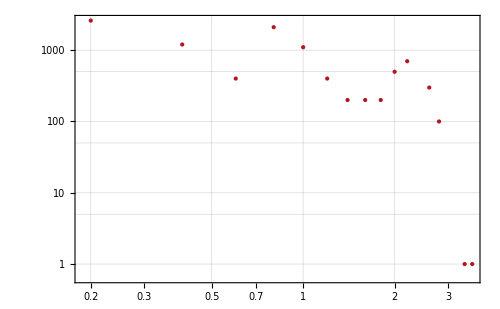
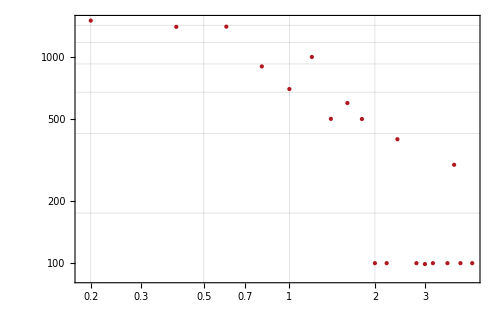
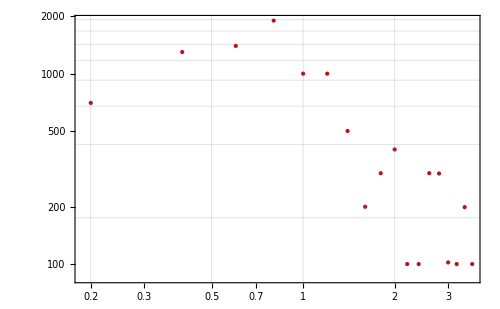
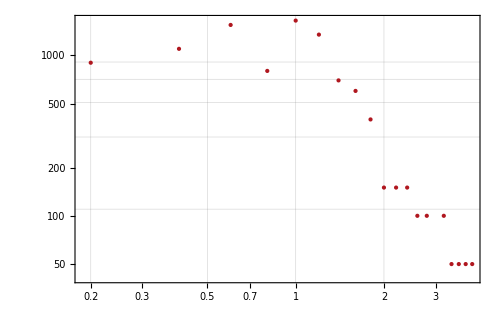
{-Graphics-64,-Graphics-230,-Graphics-329,-Graphics-407,-Graphics-409,-Graphics-454,-Graphics-466,-Graphics-497,-Graphics-518,-Graphics-525,-Graphics-554,-Graphics-762,-Graphics-815,-Graphics-939,-Graphics-982,-Graphics-1030,-Graphics-1100,-Graphics-1161,-Graphics-1196,-Graphics-1284,-Graphics-1334,-Graphics-1344,-Graphics-1382,-Graphics-1416,-Graphics-1501,-Graphics-1569,-Graphics-1570,-Graphics-1617,-Graphics-1621,-Graphics-1652,-Graphics-1707,-Graphics-1773,-Graphics-1797,-Graphics-1828,-Graphics-1880,-Graphics-1971,-Graphics-2062,-Graphics-2158,-Graphics-2244,-Graphics-2257,-Graphics-2310,-Graphics-2420,-Graphics-2701,-Graphics-2787,-Graphics-2883,-Graphics-2921,-Graphics-3121,-Graphics-3129,-Graphics-3157,-Graphics-3189,-Graphics-3227,-Graphics-3362,-Graphics-3423,-Graphics-3474,-Graphics-3523,-Graphics-3532,-Graphics-3631,-Graphics-3735,-Graphics-3796,-Graphics-3881,-Graphics-3914,-Graphics-4176,-Graphics-4195,-Graphics-4277,-Graphics-4344,-Graphics-4361,-Graphics-4607,-Graphics-4663,-Graphics-4697,-Graphics-4701,-Graphics-4713,-Graphics-4884,-Graphics-5087,-Graphics-5345,-Graphics-5439,-Graphics-5451,-Graphics-5452,-Graphics-5487,-Graphics-5565,-Graphics-5583,-Graphics-5625,-Graphics-5877,-Graphics-5879,-Graphics-5916,-Graphics-5924,-Graphics-5933,-Graphics-5961,-Graphics-6075,-Graphics-6086,-Graphics-6182,-Graphics-6207,-Graphics-6246,-Graphics-6248,-Graphics-6270,-Graphics-6309,-Graphics-6312,-Graphics-6326,-Graphics-6403,-Graphics-6493,-Graphics-6528}

```mathematica
MapThread[Labeled[#1,#2,Top]&,{histogramas,reglasRandom}]
```

```mathematica
ProgressTable[HistogramPointPlot[Abs[Returns[CATimeSeries[r,3,1,100,10000],1]],ScalingFunctions->{"Log","Log"}],{r,reglasRandom}]
```

Range::argb: Range called with 100 arguments; between 1 and 3 arguments are expected.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}